# The Origin of Structure in Biological Systems

### A Better Model for Biological Processes

What is the nature of biological processes. How do they look? What can they achieve? What happens when they go wrong?  These are such simple questions, and yet the field of biology, in my view, has largely failed to give people good answers.

In my experience, modern academic institutions are really bad at answering big questions like this, and most of the best “scientists” of our time have found ways to make progress not because of these institutions but despite them.

So okay these are bold statements, who do I think I am, right? Well, I think most biologists have largely missed a powerful new class of models: those based on simple computational rules. And because of this, they have been limited in their ability to give a good high-level description of what is going on in biology. In the past year or so, Stephen Wolfram has filled this gap and pioneered some groundbreaking computational models for biological systems. Starting as a fan of the research, and eventually becoming a collaborator, I’ve become convinced that we’ve struck gold and are now in a position to understand the high-level features of biology better than ever before.

### Computational Organisms

Again, these are big statements. So, what are our models and what claims can we make from them?

To model an “organism” we use what’s called a cellular automaton, which is just a set of updating rules, applied recursively. The rules are shown here on the right, and the result of running those rules, starting from a single red cell, is shown on the left.

```mathematica
reg[[181]]
```

{{109119604060725664814308901024268869132,4,1},195}

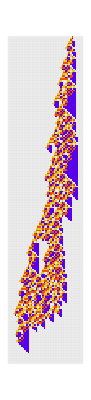
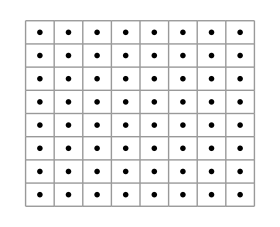

```mathematica
Row[{ArrayPlot[ArrayPad[CellularAutomaton[{109119604060725664814308901024268869132,4,1},{{1},0},200],{{0,0},{3,3}}],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],ImageSize->{Automatic,520},Mesh->All,MeshStyle->Opacity[.05]],RulePlot[CellularAutomaton[{109119604060725664814308901024268869132,4,1}],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]][[1,1,All,All,1]]//Flatten//Partition[#,UpTo[8]]&//GraphicsGrid[#,Dividers->Directive[Thin,GrayLevel[.6]],ImageSize->280]&},Spacer[20]]
```

But this isn’t just a random cellular automaton. We reached this pattern through an “evolution”, where we started from the null rule and repeatedly made random, single-bit changes (mutations) to the ruleset only keeping the changes that lead to a longer or equal finite length, here we show only the changes to the rules that we kept:

```mathematica
SymIndexMap[k_,r_]:=SymIndexMap[k,r]=With[
{tups=Tuples[Reverse[Range[0,k-1]],2r+1]},
Sort[Catenate[MapIndexed[{Position[tups,#][[1,1]],#2[[1]]}&,
GatherBy[tups,Sort[{#,Reverse[#]}]&],{2}]]]
]
```

```mathematica
SymUp[k_,r_]:=SymUp[k,r
]=SymIndexMap[k,r][[All,2]]
```

```mathematica
SymDown[k_,r_]:=SymDown[k,r
]=Values[KeySort[Map[First,
GroupBy[SymIndexMap[k,r],
Last->First]]]]
```

```mathematica
RandomRuleMutation[{rn_,k_,r_},
many_Integer:1,
OptionsPattern[{"Symmetric"->False}]
]:=Module[
{up,down,cases},
{up,down}=If[
TrueQ[OptionValue["Symmetric"]],
{SymUp[k,r],SymDown[k,r]},
{All,All}
];
cases=IntegerDigits[rn,k,k^(2r+1)][[down]];
{FromDigits[#[[up]],k],k,r}&[
MapAt[Mod[#+RandomInteger[{1,k-1}],k]&,
cases,List/@RandomSample[1;;Length[cases]-1,many]]
] 
]
```

```mathematica
evo = Module[
{deep=2000,cut=200,ru,life,evo,data},
SeedRandom[426778+181];
evo=NestList[CompoundExpression[
ru=RandomRuleMutation[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,4,1},0},deep]
];
```

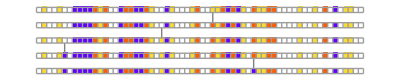
-Graphics-
⋮
-Graphics-
⋮

```mathematica
Column[{{{"[◼]", "RulesMutationPlot"}}[DeleteDuplicates[evo][[1;;5,1]],"Arrows"->"Line",ImageSize->400],"⋮",{{"[◼]", "RulesMutationPlot"}}[DeleteDuplicates[evo][[100;;104,1]],"Arrows"->"Line",ImageSize->400],"⋮"},Center]
```

And here we show the steps of the evolution where a longer pattern was discovered:

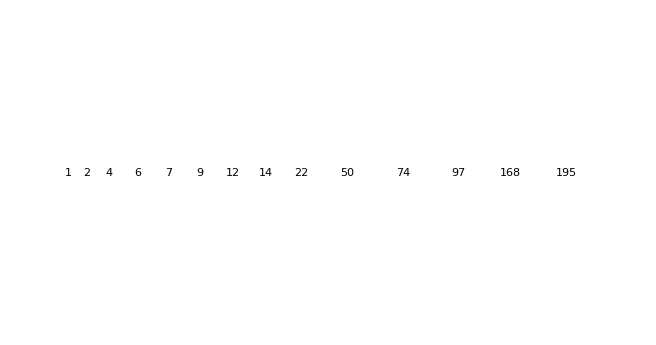

```mathematica
GraphicsRow[Labeled[{{"[◼]", "PlotCA"}}[First[#],"Trim"->{1,5},ImageSize->{Automatic,22.5 Sqrt[1+Last[#]]}],Text[Style[Last[#],Small]]]&/@Rest[evo[[ResourceFunction["ProgressiveMaxPositions"][evo[[All, -1]]]]]]]
```

So the “goal” of our organisms is to “live” as many steps as possible and then terminate. And the rules determine how the organism achieves this goal.

The similarities are already striking between this and biological evolution. We can see how the pattern builds on the ideas of its predecessors, for example the above automaton contains purple triangles throughout its history.

Zooming out, we can run multiple evolutions and see different potential evolutionary paths:

```mathematica
evos = 
Table[Module[
{deep=2000,cut=200,ru,life,evo,data},
SeedRandom[426778+i];
evo=NestList[CompoundExpression[
ru=RandomRuleMutation[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,4,1},0},deep]
], {i,{41, 43, 105}}] ;
```

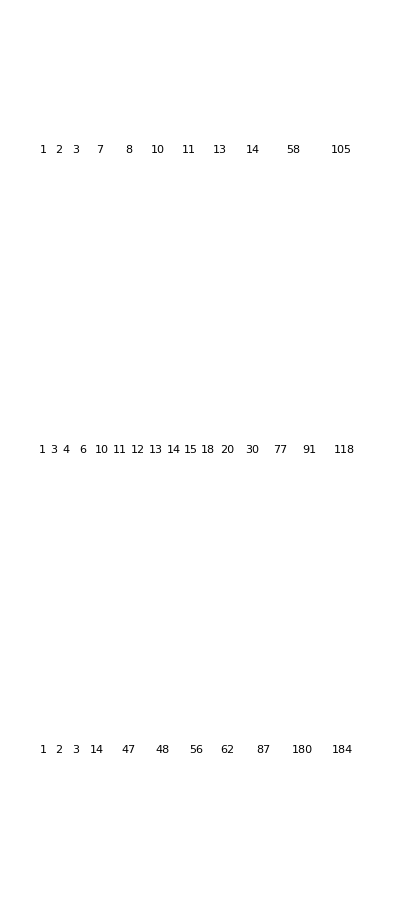

```mathematica
Column[MapThread[Function[{evo, steps}, GraphicsRow[Labeled[{{"[◼]", "PlotCA"}}[First[#],"Trim"->{1,5},ImageSize->{Automatic,22.5 Sqrt[1+Last[#]]}],Text[Style[Last[#],Small]]]&/@(Rest[evo[[ResourceFunction["ProgressiveMaxPositions"][evo[[All, -1]]]]]])]], {evos, {105, 120, 190}}],Spacer[1]]
```

And this gives us a powerful analogy to the discrete categories of organisms in the form of species that we observe in biology, and where the variation between them comes from.

### Primitive structure

But what about the nature of the actual patterns? How do these automata achieve their goal? Well, one feature that jumps out is the apparent randomness of the patterns. It’s not clear why the patterns end up terminating at the step they do. Looking closely at one of our evolved automata, we can readily see that trying to figure out why it works is like trying to jump ahead of a computational irreducible process:

```mathematica
rob = ;
reg = ;
(*See biomedicine-04 for definition*)
```

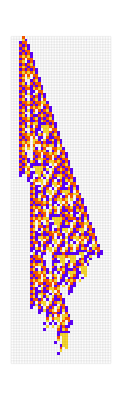

```mathematica
ArrayPlot[ArrayPad[CellularAutomaton[reg[[43, 1]],{{1},0},120],{{0,0},{3,3}}],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],ImageSize->{Automatic,520},Mesh->All,MeshStyle->Opacity[.05]]
```

But just how random are these automata, and is their any regularity or structure we can find among them? 
To answer this, we can look at a random sample of the rule space:

```mathematica
SeedRandom[5555];
GraphicsGrid[Partition[ArrayPlot[CellularAutomaton[{FromDigits[#, 4], 4, 1}, {{1}, 0}, {200, {-200, 200}}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@(Append[#, 0]&/@RandomChoice[{0, 1, 2, 3}, {15 , 4^(2*1+1) - 1}]), 3], ImageSize->{600, Automatic}]
```

-Graphics-

And compare that with a random sample of our evolved automata:

```mathematica
rob = ;
reg = ;
(*See biomedicine-04 for definition*)
```

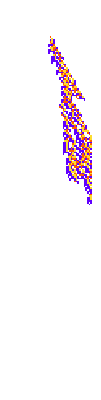

```mathematica
SeedRandom[6666];
GraphicsGrid[Partition[ArrayPlot[CellularAutomaton[#,{{1}, 0}, {200, {-25, 25}}], ColorRules-> {{"[◼]", "CustomStyleData"}}["Colors"]]& /@RandomSample[reg[[All, 1]], 16], 8]]
```

What becomes obvious here is that because the automata are required to terminate, we have selected for “skinnier” patterns, with slower “growth-rates” as measured by the width of the colored cell range at each step. Here is a comparison between the growth rates for the random vs. evolved:

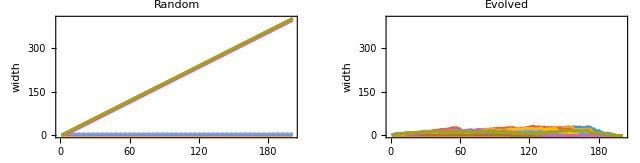

```mathematica
SeedRandom[6666];
GraphicsRow[{
ListLinePlot[If[Length[#]===0,0,Last[#]-First[#]+1]&[{{"[◼]", "nonzeroRange"}}[#]]&/@CellularAutomaton[{FromDigits[#, 4], 4, 1},{{1}, 0}, 200]&/@(Append[#, 0]&/@RandomChoice[{0, 1, 2, 3}, {10 , 4^(2*1+1) - 1}]), PlotHighlighting->None,  Frame->True, AspectRatio->.4, FrameLabel->{"steps", "width"}, PlotLabel->"Random"],
ListLinePlot[If[Length[#]===0,0,Last[#]-First[#]+1]&[{{"[◼]", "nonzeroRange"}}[#]]&/@CellularAutomaton[#,{{1}, 0}, 200]&/@RandomSample[reg[[All, 1]], 10], PlotRange->400, Filling->Bottom, PlotHighlighting->None, Frame->True, AspectRatio->.4, FrameLabel->{"steps", "width"}, PlotLabel->"Evolved"]

}]
```

So clearly the evolved patterns are not completely random in their construction. And we can think of this as the beginnings of structure in our computational biological universe, where the fitness landscape pushes organisms away from complete randomness, into specific niches in order to solve a particular problem.

So this is an example of the formation of high-level structure. But what about at the level of the rules? Can we find any regularities there?

To do this, we can look at the frequencies of various colors for all the possible rules in the random and evolved groups:

```mathematica
Column[MapThread[Function[{digs,label}, With[{aps = Rasterize[ArrayPlot[List/@#,ImageSize->{10, 25}, ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"](*, Mesh->True, MeshStyle->Opacity[.4]*)]]& /@ RuleTuples[4, 1]}, BarChart[BinCounts[#, {0, 4, 1}]&/@Transpose[digs], ChartLayout->"Stacked", ChartBaseStyle->EdgeForm[Thickness[.1]], ChartStyle->(Directive[EdgeForm[Directive[Opacity[1], Gray]], #]&)/@ {{"[◼]", "CustomStyleData"}}["Colors"][[All, 2]], ChartLabels->{aps, None}, LabelingSize->35, AspectRatio->.4, ImageSize->{600, Automatic}, Frame->True, FrameLabel->{"rule", "counts"},PlotLabel->label]]],
{{(Append[#, 0]&/@RandomChoice[{0, 1, 2, 3}, {200 , 4^(2*1+1) - 1}]),Module[{digits, n, k, r},
{n, k, r} =interpretrule[#];
digits = IntegerDigits[n, k, k^(2r+1)]]&/@ reg[[All, 1]]}, {"Random", "Evolved"}}]]
```

-Graphics-

So on the y-axis here we have the counts of the different output colors for each rule. As you’d expect, the random group basically has an equal distribution of the different output colors for each rule. But with the evolved group, we can see that certain rules have an unequal distribution, and in particular, keeping in mind our growth inhibition plots, we can notice that the rules with two white-cells on the edge always have a higher probability of outputting a white cell. These rules, occur on the borders of the pattern, and therefore are important for determining the growth rate of the pattern. Here we show these “edge-rules” highlighted in red:

```mathematica
SeedRandom[6666];

GraphicsRow[Function[ca, 
Module[{b = Array[0 &, {Length[ca], Length[ca[[1]]]}]}, 
gray = ReplacePart[b, Thread[bodyidxs[ca]-> 1]];
redidxs = 
MapIndexed[Function[{val, idx}, {idx[[1]], #}&/@ val], DeleteCases[(Flatten/@Function[row, If[# === {}, {}, Range@@@#]&[SequencePosition[row, #]]&/@ edgerules]/@ca), {}]];
ArrayPlot[ReplacePart[gray, Thread[redidxs->2]], ColorRules->{0->White, 1->LightGray, 2->Red}]
]]/@ (CellularAutomaton[#, {{1}, 0}, 200]&/@RandomSample[reg[[All, 1]], 10])]
```

-Graphics-

So interestingly, what we’re seeing here is the development of a low-level mechanism within our automata, that helps the “organism” achieve its goal. In biological terms, this is analogous to a particular gene being selected for because it say, inhibits unhealthy growth.

### Squeezing irreducibility out of the system

Okay, so we’ve identified some regularity and structure at multiple scales within this evolved group, but there is still plenty of irreducibility within these systems. For example, the “growth patterns” within the “body” of the automaton still look very random, and the details of why they grow and why they stop growing are very complicated. And this is reflected in the frequencies of the “inner-rules”, which from the plot above we can see look very much like the random group.

So how can we push our automata further away from this irreducibility? Well, one difference between our evolution here and real evolution, is that organisms in biology have to be able to achieve their goal even when the details of the environment change. For example, the exact locations of the cells within a frog embryo may change, but it still needs to be able to grow into a tadpole and then a frog.

In the evolution we ran previously, the “environment” is always a blank slate of white cells. You may imagine, that forcing our automata to achieve their goal in multiple different environments could lead to more purposeful mechanisms within the system.

To test this, we can run an evolution very similar to our first one, but instead of running the rules only in an all-white environment at each step, we can run them in multiple environments, each differing by a single cell. So here is an example step in one of our “perturbed evolutions”, with an arrow pointing to the cell that was changed:

```mathematica
SymIndexMap[k_,r_]:=SymIndexMap[k,r]=With[
{tups=Tuples[Reverse[Range[0,k-1]],2r+1]},
Sort[Catenate[MapIndexed[{Position[tups,#][[1,1]],#2[[1]]}&,
GatherBy[tups,Sort[{#,Reverse[#]}]&],{2}]]]
]
```

```mathematica
SymUp[k_,r_]:=SymUp[k,r
]=SymIndexMap[k,r][[All,2]]
```

```mathematica
SymDown[k_,r_]:=SymDown[k,r
]=Values[KeySort[Map[First,
GroupBy[SymIndexMap[k,r],
Last->First]]]]
```

```mathematica
RandomRuleMutation[{rn_,k_,r_},
many_Integer:1,
OptionsPattern[{"Symmetric"->False}]
]:=Module[
{up,down,cases},
{up,down}=If[
TrueQ[OptionValue["Symmetric"]],
{SymUp[k,r],SymDown[k,r]},
{All,All}
];
cases=IntegerDigits[rn,k,k^(2r+1)][[down]];
{FromDigits[#[[up]],k],k,r}&[
MapAt[Mod[#+RandomInteger[{1,k-1}],k]&,
cases,List/@RandomSample[1;;Length[cases]-1,many]]
] 
]
```

```mathematica
SeedRandom[426778+132];
perts = Reap[bye = NestList[CompoundExpression[
ru=RandomRuleMutation[First[#]],
ca = CellularAutomaton[ru,{{1}, 0}, {200, All}];
lt = TestCALifeTime[ca];
If[lt == -Infinity, #,
(*pcas = Table[PerturbCA[{ca, ru}], Ceiling[lt / 20]];*)
pcas = Table[PerturbedCellularAutomaton[ru,{{1}, 0},{200, {-200, 200}}],5];
Sow[{ru, pcas[[All, 2]]}];
fitness = Min[Join[{lt}, TestCALifeTime/@ pcas]];
If[fitness>=Last[#],{ru,fitness},#]
]]&,{{0,4,1},0},2000]][[2, 1]];
```

```mathematica
kept = Select[perts, MemberQ[bye[[All, 1]],#[[1]]]&] ;
```

```mathematica
GraphicsRow[Function[{ru, perts}, With[{ca = PerturbedCellularAutomaton[ru, {{1}, 0}, {28,  {-200, 200}}, #]},Labeled[PlotCA[ca, Mesh->True],Text[ TestCALifeTime[ca]]]]&/@ Prepend[perts, <||>]]@@kept[[104]]]
```

-Graphics-

And we now define our fitness as the minimum length of all the resulting patterns (including the unperturbed one). So in the above case the fitness would be fifteen. One important note is that if any of the patterns go past the cutoff length (we used two-hundred in the evolution below) then the fitness is zero. So this case for example would have a fitness of zero:

```mathematica
GraphicsRow[Function[{ru, perts}, With[{ca = PerturbedCellularAutomaton[ru, {{1}, 0}, {200,  {-200, 200}}, #]},Labeled[PlotCA[ca],Text[ TestCALifeTime[ca]]]]&/@ Prepend[perts, <||>]]@@perts[[750]]]
```

-Graphics-

And because of that, we are putting pressure on the system to avoid “blowing up”, and we’ll see later how it adapts to this challenge.

So what is the result from our robust evolution? Here are the resulting lifetimes from a regular and a perturbed evolution:

```mathematica
Column[MapThread[Function[{idxs, labs}, 
ListPlot[MapIndexed[
Module[{ca = CellularAutomaton[#, {{1}, 0}, 200], lt},
lt = TestCALifeTime[ca];
If[MemberQ[r, #2[[1]]],Callout[lt, PlotCA[ArrayPad[#, 1]&/@ca,"Trim"->{None, 5}, ImageSize->{Automatic,25 Sqrt[1+lt]}], LabelVisibility->All], TestCALifeTime[ca]]]&, idxs], LabelingSize->75, Filling->Bottom, AspectRatio->.4, ImageSize->{600, Automatic}, PlotRange->{{0, 200}, {0, 250}}, PlotLabel->labs, Frame->True, FrameLabel->{"pattern", "lifetime"}]], {{reg[[sireg, 1]], rob[[sortedidxs, 1]]}, {"Regular Evolution", "Perturbed Evolution"}}]]
```

-Graphics-
-Graphics-

So first off, the length of the automata in the perturbed evolution are quite a bit shorter, which makes sense because, as we mentioned above, any perturbed pattern that runs past the cut-off length will cause the whole group’s fitness to be zero. So it gets harder and harder to increase the length of the automaton as you approach the end-line. But, despite this, a few of our patterns have managed to still live quite long, here is the top ten longest lived patterns from our perturbed evolution:

```mathematica
With[{cas = CellularAutomaton[#, {{1}, 0}, {200}]&/@ rob[[All, 1]]},
GraphicsRow[
Labeled[PlotCA[ArrayPad[#, 1]&/@#, Frame->True], TestCALifeTime[#]]&/@TakeLargestBy[cas, TestCALifeTime, 10], ImageSize->{600, Automatic}]
]
```

-Graphics-

But we don’t just care about the lifetime, we also want to see the lifetime under perturbation. Here we show the automata with the highest mean lifetime under perturbation, along with their respective lifetime distributions:

```mathematica
l1 = Select[rob, TestCALifeTime[CellularAutomaton[#[[1]], {{1}, 0}, 200]]>100&];
```

```mathematica
samplts = ParallelMap[Table[TestCALifeTime[{{"[◼]", "PerturbedCellularAutomaton"}}[#,{{1},0},{200,{-100,100}}]], 200]&,l1[[All, 1]]];
```

```mathematica
Iconize[samplts]
```

```mathematica
zd = (samplts /. -Infinity->0);
```

```mathematica
bmi = With[{zd = (samplts /. -Infinity->0)}, 
ReverseSortBy[Range[Length[l1]],Mean[zd[[#]]]&]];
```

```mathematica
means = N[Mean/@ zd];
```

```mathematica
GraphicsGrid[Partition[MapIndexed[BarChart[ReplacePart[#,10->Callout[#[[10]], PlotCA[l1[[bmi[[#2[[1]]]], 1]], "Trim"->{1, 3}], Above, Appearance->None]] ,PlotRange->100,Frame->True, FrameTicks->{{If[#2[[1]] == 1 || #2[[1]] == 4, Automatic, None],Automatic}, {If[4 <=#2[[1]] <= 6,  Table[{i, 5i}, {i, 0,50, 10}], None], Automatic}}, BarSpacing->None,ImageSize->{If[#2[[1]] == 1 || #2[[1]] == 4,285, 280], Automatic} , LabelingSize->100, PlotRange->150, PlotRangePadding->{Automatic, 0},
Epilog->{Dotted, Red, Line[{{means[[bmi[[#2[[1]]]]]]/5, 100}, {means[[bmi[[#2[[1]]]]]]/5, 0}}]}
]&, 
MapAt[Style[#,Red]&, BinCounts[#, {5}]&/@(samplts[[bmi[[;;6]]]]/.-Infinity->210), {All, -1}]], 3], Spacings->0, ImageSize->{600, Automatic}]
```

-Graphics-

So the big yellow automaton, is far more robust than the others. Why is this? Looking at some sample perturbations, we can see that many of the changes have little effect on the pattern.

```mathematica
GraphicsRow[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[l1[[bmi[[1]], 1]],{{1}, 0}, {200, {-200, 200}}, #] ,"ArrowSize"->Small]&/@{<||>,<|{89,201}->1|>,<|{82,206}->2|>,<|{135,215}->1|>,<|{105,213}->2|>,<|{22,199}->0|>,<|{40,202}->0|>,<|{64,197}->2|>, <|{83,215}->0|>}]
```

-Graphics-

Running the rule from various initial conditions we can see it is an attractor, meaning that most of the time it results in a similar shape despite changes in the initial state:

```mathematica
GraphicsRow[Table[PlotCA[CellularAutomaton[l1[[bmi[[1]], 1]], {RandomChoice[{0, 1, 2, 3}, 30], 0}, 250]], 5]]
```

-Graphics-

So we can think of this rule like an approximate funnel, depending on where you start, the detail of how you get to the bottom will change, but the final location will not vary much.

More specifically, on the left hand side there is some probability of reaching the diagonal purple repeating sequence. Once you hit that sequence it repeats at an angle, which “dominates” the yellow section and leads to what we can think of as a “programmed death”:

```mathematica
GraphicsRow[{PlotCA[CellularAutomaton[l1[[bmi[[1]], 1]], {{1}, 0}, {{20, 50}, {-50, 50}}]], PlotCA[CellularAutomaton[l1[[bmi[[1]], 1]], {{1}, 0}, {{160, 190}, {-50, 50}}]]}]
```

-Graphics-

Down the middle, the pattern tend towards yellow, and importantly, within the yellow, only trivial patterns can “escape”, almost like molasses:

```mathematica
GraphicsRow[Table[PlotCA[CellularAutomaton[l1[[bmi[[1]], 1]], {RandomChoice[{0, 1, 2, 3}, 30], 3}, 50]], 5]]
```

-Graphics-

On the right hand side each red streak “bumps” the edge, extending the lifetime only slightly, until there are no more streaks, and the yellow section proceeds straight downward, eventually terminating:

```mathematica
PlotCA[CellularAutomaton[l1[[bmi[[1]], 1]], {{1}, 0}, {{50, 100}, {-5, 30}}], "Trim"->{None, None}]
```

-Graphics-

And it is these mechanisms that enable it to be an attractor. But being an attractor alone isn’t enough. For instance, trivially, the null rule is an attractor:

```mathematica
PlotCA[CellularAutomaton[{0, 4, 1}, {{1}, 0}, {3, {-3, 3}}], ImageSize->75]
```

-Graphics-

But what we’re asking it to do is more specific then just attraction. It actually needs to trace a path from a simple state (the “seed” shown above) to a more complex one, (the “growth phase”) and then back to a simple all-white state. And the key feature of this automaton is that goes quickly from simple to complex and back to simple, which is what enables it to be robust. To make this point concrete we can attempt to compress each row, and use the resulting size as a measure of the row’s complexity, then, we can graph that over time and get a sense of the “flow of complexity” within the system:

to be a slow attractor. So we want it to start with the null rule, go to some “colored” state, and then attract to white. But the interesting thing is, this rule finds a good solution to this problem, by attracting to a very simple “all-yellow” state, and then goes to white. And because of this, any changes made to it in the all-yellow section can easily be absorbed, because it’s already so low into a “valley of simplicity”. To make this idea more concrete we can

. It n it’s not a “quick” attractor, it has a yellow phase and then a white

once you hit that sequence it is like a programmed

Zooming in, we see that when we perturb the big yellow blade there is a small change to to the system in the form of a diagonal red streak, but the right edge “absorbs” it resulting in only a slightly longer lifetime:

```mathematica
Module[{cas = {{"[◼]", "PerturbedCellularAutomaton"}}[l1[[bmi[[1]], 1]],{{1}, 0}, {#, {-200, 200}}, <|{82 ,206}->2|>]&/@ {200, {75, 110}}},
{{left, right}, bottom} = gettrimoffsets[cas[[2, 1]], {1, None}];
GraphicsRow[{ {{"[◼]", "PlotCA"}}[cas[[1]], "ArrowSize"->Small],  {{"[◼]", "PlotCA"}}[cas[[2, 1]],"Graphics"->getarrow[cas[[2, 1]], {82  - 75,206}, left, bottom, "Left"], ImageSize->200]}, Alignment->Center]]
```

-Graphics-

And this actually works for any color change or any location within the blade:

```mathematica
GraphicsRow[Module[{ca = First[{{"[◼]", "PerturbedCellularAutomaton"}}[l1[[bmi[[1]], 1]],{{1}, 0}, {{75, 110}, {-200, 200}}, <|#|>]]},
{{left, right}, bottom} = gettrimoffsets[ca, {1, None}]; {{"[◼]", "PlotCA"}}[ca , "Graphics"->getarrow[ca, {#[[1, 1]] - 75,#[[1, 2]] + 1}, left, bottom, "Left"]]]&/@ {{82 ,206}->2,{85 ,215}->0, {95 ,206}->1}, ImageSize->{675, Automatic}]
```

-Graphics-

And the fact that the yellow blade is simple means that

But it’s not it’s simplicity that makes it robust. It’s just based on the fact that it’s an attractor. I mean maybe it helps that it’s

And not only that but the we can even do multiple perturbations to the blade:

And there are two key features that make this possible. First, the simplicity of the yellow section means that there are limited “failure-states” of the system, so even if we move the perturbation location, or change the color, there are only nine potential new rules that can come about:

```mathematica
GraphicsGrid[Transpose[Partition[Show[#, ImageSize->Small]&/@(RulePlot[CellularAutomaton[l1[[bmi[[1]], 1]]],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]][[1,1,All,All,1]]//Flatten)[[{2, 3, 4, 5, 9, 13, 17, 33, 49, 1}]], 3]], Dividers->Directive[Thin,GrayLevel[.6]],ImageSize->280]
```

-Graphics-

And when these rules do come about , they are quickly transformed into the red streak pattern. Here we show the causal graph between rules in the case of a purple perturbation:

```mathematica
subs = getsubs[l1[[bmi[[1]], 1]]];
```

```mathematica
nextrus[rus_]:= 
Partition[ArrayPad[Replace[#, subs]&/@ rus, 1, 3], 3, 1]
```

```mathematica
init = {3, 3, 3, 3, 2, 3, 3, 3, 3};
```

```mathematica
tab = NestList[nextrus, ArrayPad[Partition[init, 3, 1], {1}, {{3, 3, 3}}], 6];
```

```mathematica
Graph[Catenate[Table[{{i, j}, tab[[i, j]]}, {i, 1, Length[tab]}, {j, 1,Length[tab[[1]]]}]], Flatten[Table[{{i, j}, tab[[i, j]]}->{{i + 1, #}, tab[[i + 1, #]]}&/@ Select[{j -1, j, j + 1}, 1<= # <= Length[tab[[1]]]&], {i,1, Length[tab] - 1}, {j, 1, Length[tab[[1]]]}]], VertexShapeFunction->(Inset[PlotCA[{#2[[2]]}, ImageSize->30], #1]&), VertexCoordinates->Catenate[Table[{j, i}, {i,Length[tab], 1, -1}, {j,1, Length[tab[[1]]]}]]]
```

-Graphics-

And here is the graph for a white perturbation:

```mathematica
init = {3, 3, 3, 3, 0, 3, 3, 3, 3};
```

```mathematica
tab = NestList[nextrus, ArrayPad[Partition[init, 3, 1], {1}, {{3, 3, 3}}], 6];
```

```mathematica
Graph[Catenate[Table[{{i, j}, tab[[i, j]]}, {i, 1, Length[tab]}, {j, 1,Length[tab[[1]]]}]], Flatten[Table[{{i, j}, tab[[i, j]]}->{{i + 1, #}, tab[[i + 1, #]]}&/@ Select[{j -1, j, j + 1}, 1<= # <= Length[tab[[1]]]&], {i,1, Length[tab] - 1}, {j, 1, Length[tab[[1]]]}]], VertexShapeFunction->(Inset[PlotCA[{#2[[2]]}, ImageSize->30], #1]&), VertexCoordinates->Catenate[Table[{j, i}, {i,Length[tab], 1, -1}, {j,1, Length[tab[[1]]]}]]]
```

-Graphics-

So we can clearly see the white and purple perturbations lead to the same five rules, which then lead to the red streak pattern. While the actual mechanism for how these five rules reach the red streak rule is not really reducible beyond saying, “because they do”, the point is that because this yellow section is uniform, the system can use this mechanism even if the details of the perturbation change. And in fact, this doesn’t work as well if we perturb in the more complex parts of the system:

```mathematica
Module[{rps = Transpose[{RandomInteger[{1, 15}, 10], RandomInteger[{195, 205}, 10]}]},GraphicsRow[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[l1[[bmi[[1]], 1]],{{1}, 0}, {200, {-200, 200}}, #->"Random"], "ArrowSize"->Small]&/@ rps]]
```

-Graphics-

```mathematica
Module[{rps = Transpose[{RandomInteger[{1, 15}, 10], RandomInteger[{195, 205}, 10]}]},GraphicsRow[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[l1[[bmi[[1]], 1]],{{1}, 0}, {200, {-200, 200}}, #->"Random"], "ArrowSize"->Small]&/@ rps]]
```

```mathematica
Table[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[l1[[bmi[[1]], 1]],{{1}, 0}, {200, {-200, 200}}, {RandomChoice, -1}, "Body"->True], "ArrowSize"->Small], 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

But the fact that the pattern is uniform, means it can use this same mechanism, even if the details of the perturbation change.

And other than the fact that the red streak rule, and the all yellow rules produce themselves, the exact mechanism for how this set of rules goes from the purple perturbation to the red streak is I suspect irreducible.

Now, the reason “why”  these particular rules lead to the red streak

it is the interaction of these rules, that leads to

And there are two key features that make this possible. First, the simplicity of the yellow section means that there are limited “failure-states” of the system.

And second, a mechanism for quickly “compressing” the error before it can affect the lifetime. 

Well, we can see 


And this makes it possible for the system to quickly “compress” the error into a manageable size, which limits its effect.

so even if we move the perturbation location, or change the color of the cell